```mathematica
SetDirectory[NotebookDirectory[]]
<<KnotTheory`
```

/home/dj/CLionProjects/c-flypes

Get::path: ParentDirectory[File] in $Path is not a string.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ParentDirectory[File],KnotTheory].

FileInformation::badfile: The specified argument ToFileName[ParentDirectory[File],KnotTheory] should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory].

FileInformation::badfile: The specified argument ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory] should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory].

General::stop: Further output of ToFileName::strse will be suppressed during this calculation.

FileInformation::badfile: The specified argument ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory] should be a valid string or File.

General::stop: Further output of FileInformation::badfile will be suppressed during this calculation.

ReplaceAll::reps: {AbsoluteFileName→/usr/local/Wolfram/Mathematica/12.0/AddOns/ExtraPackages/KnotTheory,«35»,FileInformation[ToFileName[ToFileName[{File/.{Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],«10»,Rule[«2»],Rule[«2»],Rule[«2»],FileInformation[«1»],FileInformation[«1»],FileInformation[«1»],FileInformation[«1»],FileInformation[«1»],FileInformation[«1»],FileInformation[«1»],FileInformation[«1»],FileInformation[«1»]},…}],…]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ParentDirectory::nums: Argument File/.{AbsoluteFileName→/usr/local/Wolfram/Mathematica/12.0/AddOns/ExtraPackages/KnotTheory,BlockCount→8,BlockSize→4096,«32»,FileInformation[ToFileName[ToFileName[{File/.{«34»},WikiLink,mathematica}],KnotTheory]],FileInformation[ToFileName[ToFileName[{File/.{«34»},QuantumGroups}],KnotTheory]]} should be a positive machine-size integer, a nonempty string, or a File specification.

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

Get::path: ParentDirectory[File] in $Path is not a string.

General::stop: Further output of Get::path will be suppressed during this calculation.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol CreateWikiConnection in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,WikiStringCases,WikiAllPages}] has already been declared.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol WikiGetPageText in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,WikiStringCases,WikiAllPages}] has already been declared.

Get::noopen: Cannot open WikiLink`.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

DeclarePackage::aldec: Symbol WikiGetPageTexts in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,WikiStringCases,WikiAllPages}] has already been declared.

General::stop: Further output of DeclarePackage::aldec will be suppressed during this calculation.

```mathematica
Export["knot_txt_files/knot_4_1.txt",PD[Knot[4,1]]]
```

KnotTheory::loading: Loading precomputed data in PD4Knots`.

knot_txt_files/knot_4_1.txt

```mathematica
Export["knot_txt_files/knot_6_1.txt",PD[Knot[6,1]]]
```

knot_txt_files/knot_6_1.txt

```mathematica
Export["knot_txt_files/knot_15_70.txt",PD[Knot[15,Alternating,70]]]
```

knot_txt_files/knot_15_70.txt

```mathematica
Export["knot_txt_files/knot_16_1.txt",PD[Knot[16,Alternating,1]]]
```

KnotTheory::loading: Loading precomputed data in KnotTheory/16A.dts.

KnotTheory::credits: The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005.

knot_txt_files/knot_16_1.txt

```mathematica
Length@GetAllFlypesFromPD[PD@Knot[6,1]]
```

20

```mathematica
Length@GetAllFlypesFromPD[PD@Knot[15,Alternating,70]]
```

54

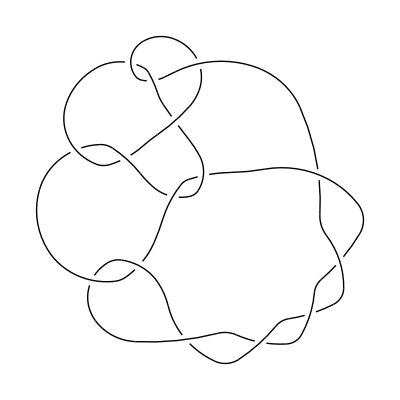

```mathematica
DrawPD[PD@Knot[15,Alternating,70],{Gap->0.03}]
```

```mathematica
Length/@GetAllFlypesFromPD[PD@Knot[6,1]][[All,1]]
```

{2,2,2,2,2,2,3,3,3,3,3,3,4,4,4,4,4,4,4,4}

```mathematica
Length[GetAllTanglesFromPD[PD@Knot[4,1]]]
```

2

```mathematica
Length[GetAllTanglesFromPD[PD@Knot[6,1]]]
```

12

```mathematica
Length[GetAllFlypesFromPD[PD@Knot[16,Alternating,1]]]
```

22

```mathematica
MatrixForm@({ParallelCheck[Knot[6,1],#⟦1⟧,#⟦2⟧],#⟦2⟧,#⟦1⟧}&/@GetAllFlypesFromPD[PD@Knot[6,1]])
```

(False | {11,6,12,7} | {{1,4,2,5},{5,12,6,1}}
True | {5,12,6,1} | {{7,10,8,11},{11,6,12,7}}
False | {1,4,2,5} | {{9,3,10,2},{3,9,4,8}}
False | {7,10,8,11} | {{9,3,10,2},{3,9,4,8}}
False | {1,4,2,5} | {{11,6,12,7},{5,12,6,1}}
False | {7,10,8,11} | {{11,6,12,7},{5,12,6,1}}
False | {7,10,8,11} | {{1,4,2,5},{5,12,6,1},{11,6,12,7}}
False | {7,10,8,11} | {{1,4,2,5},{9,3,10,2},{3,9,4,8}}
False | {5,12,6,1} | {{1,4,2,5},{9,3,10,2},{3,9,4,8}}
False | {1,4,2,5} | {{7,10,8,11},{3,9,4,8},{9,3,10,2}}
False | {11,6,12,7} | {{7,10,8,11},{3,9,4,8},{9,3,10,2}}
False | {1,4,2,5} | {{7,10,8,11},{11,6,12,7},{5,12,6,1}}
False | {7,10,8,11} | {{1,4,2,5},{5,12,6,1},{9,3,10,2},{3,9,4,8}}
False | {11,6,12,7} | {{1,4,2,5},{5,12,6,1},{9,3,10,2},{3,9,4,8}}
False | {3,9,4,8} | {{1,4,2,5},{5,12,6,1},{11,6,12,7},{7,10,8,11}}
False | {9,3,10,2} | {{1,4,2,5},{5,12,6,1},{11,6,12,7},{7,10,8,11}}
False | {5,12,6,1} | {{1,4,2,5},{9,3,10,2},{3,9,4,8},{7,10,8,11}}
False | {11,6,12,7} | {{1,4,2,5},{9,3,10,2},{3,9,4,8},{7,10,8,11}}
False | {1,4,2,5} | {{7,10,8,11},{11,6,12,7},{3,9,4,8},{9,3,10,2}}
True | {5,12,6,1} | {{7,10,8,11},{11,6,12,7},{3,9,4,8},{9,3,10,2}})